# EIWL Sections 35, 36

## Section 35

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
Cases[Interpreter["University"][StringJoin["U of ",#]&/@ToUpperCase[Alphabet[]]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
Cases[Interpreter["Movie"][CommonName/@],_Entity]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"a","i","l","m"}]],_Entity]
```

{Alim,Amli,Balm,Ilam,Lami,Lima,Lamai,Mali,Milah,Mali}

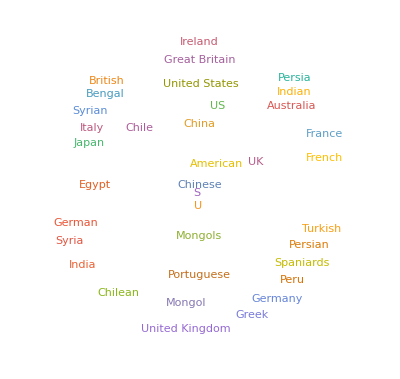

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
TextCases["She sells seashells by the seashore","Noun"]
```

{seashells,seashore}

```mathematica
Length[TextCases[StringTake[WikipediaData["computers"],1000],#]]&/@{"Noun","Verb","Adjective"}
```

{51,25,21}

```mathematica
TextStructure[TextSentences[WikipediaData["computers"]][[1]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
TakeLargest[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]],10]
```

<|the→573,and→319,a→269,to→248,she→203,of→194,was→166,Alice→161,in→155,it→154|>

```mathematica
CommunityGraphPlot[First[TextStructure[TextSentences[WikipediaData["language"]][[1]],"ConstituentGraphs"]]]
```

-Graphics-

```mathematica
Length[TextCases[WordList[],#]]&/@{"Noun","Verb","Adjective","Adverb"};
```

$Aborted

```mathematica
(*This won't evaluate, but I think it's right*)
```

```mathematica
WordTranslation[#,"French"]&/@IntegerName[Range[2,10]]
```

{{deux},{trois},{quatre},{cinq},{six},{sept},{huit},{neuf},{dix}}

## Section 36

```mathematica
CloudPublish[Style[RandomInteger[1000],100]]
```

CloudObject[https://www.wolframcloud.com/obj/f6afd07e-4df4-4887-892f-6e8e0e3dbd2a]

```mathematica
CloudPublish[FormFunction[{"x"->"Number"},#x^#x&]]
```

CloudObject[https://www.wolframcloud.com/obj/2f383d9f-abbe-4e93-b80d-6b0f813fc7fd]

```mathematica
CloudPublish[FormFunction[{"x"->"Number","y"->"Number"},#x^#y&]]
```

CloudObject[https://www.wolframcloud.com/obj/a4115020-90d6-4ce4-a5f9-335f126d0522]

```mathematica
CloudPublish[FormFunction[{"topic"->"String"},WordCloud[WikipediaData[#topic]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/2b38d0d7-f40f-475b-b021-c800d88c814a]

```mathematica
CloudPublish[FormFunction[{"word"->"String"},Style[StringReverse[#word],50]&]]
```

CloudObject[https://www.wolframcloud.com/obj/b55dad30-b56c-4ad8-9f1d-2e101ff67818]

```mathematica
FormFunction[{"sides"->"Integer"},Graphics[Style[RegularPolygon[#sides],RandomColor[]]]&]
```

FormFunction[]

```mathematica
CloudPublish[FormFunction[{"where"->"Location","number"->"Integer"},GeoListPlot[GeoNearest["Volcano",#where,#number]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/cd1557c6-6ea3-4759-af84-b5eda979d062]